```mathematica
boxlength = 40;
σ=1;
Δx=0.04;
Δt=0.002;
tmax=3;
x0=-10;
barrierwidth=4;
k0=10;
V0=k0^2/2;
α=I Δt/(4(Δx)^2);
```

```mathematica
Unprotect[HeavisideTheta]
HeavisideTheta[0.]=1
Protect[HeavisideTheta]
```

{HeavisideTheta}

1

{HeavisideTheta}

```mathematica
psi[x_,0]=Exp[I k0 (x-x0)]Exp[-(x-x0)^2/(2σ^2)] ;
psilist={};
psi0=Table[{x,psi[x,0]},{x,-boxlength/2,boxlength/2,Δx}];
AppendTo[psilist,psi0];
V=Table[V0*HeavisideTheta[barrierwidth/2-x]*HeavisideTheta[x+barrierwidth/2],{x,-boxlength/2,boxlength/2,Δx}];
β=Table[I Δt/2(1/(Δx)^2+V[[i]]),{i,1,Length[V]}];
```

```mathematica
Length[psi0]
```

1001

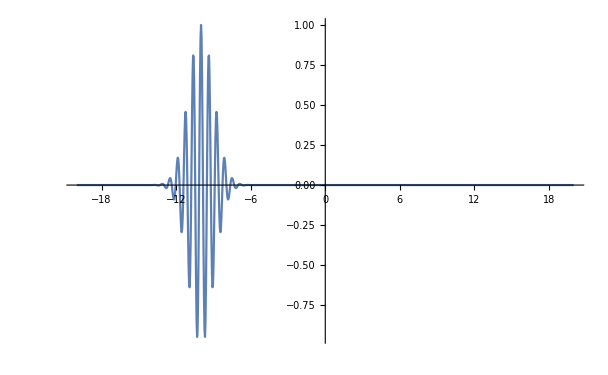

```mathematica
ListPlot[Re[psi0],PlotRange->All,Joined->True]
```

```mathematica
D1=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
D2=Table[0,{i,1,boxlength/Δx+1},{j,1,boxlength/Δx+1}];
```

```mathematica
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α,If[i==Floor[boxlength/Δx+1],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]],D1[[i,i-1]]=α;D1[[i,i]]=1-β[[i]];D1[[i,i+1]]=α]]]
For[i=1,i≤boxlength/Δx+1,i++,If[i==1,D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α,If[i==Floor[boxlength/Δx+1],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]],D2[[i,i-1]]=-α;D2[[i,i]]=1+β[[i]];D2[[i,i+1]]=-α]]]
```

```mathematica
D2inv=Inverse[D2]
```

{{0.718575-0.393836 ⅈ,0.176875+0.112889 ⅈ,-0.00358095+0.0536118 ⅈ,-0.0124795+0.00579408 ⅈ,-0.00283699-0.00208923 ⅈ,0.000119988-0.000894188 ⅈ,0.000215561-0.0000831071 ⅈ,0.000045192+0.000038177 ⅈ,-3.01088×10^-6+0.0000148467 ⅈ,983,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},999,{0.+0. ⅈ,999,0.718575-1}}
 |  |  |  |

```mathematica
psilist
```

```mathematica
Transpose[Last[psilist]][[2]]
```

{1.6632×10^-22+9.76653×10^-23 ⅈ,1.71658×10^-22+2.30636×10^-22 ⅈ,1.01638×10^-22+4.15633×10^-22 ⅈ,-1.01396×10^-22+6.27636×10^-22 ⅈ,-5.01131×10^-22+7.99018×10^-22 ⅈ,-1.1445×10^-21+8.00982×10^-22 ⅈ,-2.02008×10^-21+4.31891×10^-22 ⅈ,-2.99531×10^-21-5.74108×10^-22 ⅈ,-3.7371×10^-21-2.4988×10^-21 ⅈ,-3.63359×10^-21-5.52885×10^-21 ⅈ,-1.75396×10^-21-9.56144×10^-21 ⅈ,3.09222×10^-21-1.39211×10^-20 ⅈ,1.21114×10^-20-1.70161×10^-20 ⅈ,2.60019×10^-20-1.60214×10^-20 ⅈ,4.40734×10^-20-6.76117×10^-21 ⅈ,6.30085×10^-20+1.59398×10^-20 ⅈ,7.54236×10^-20+5.70735×10^-20 ⅈ,6.86438×10^-20+1.19055×10^-19 ⅈ,2.44622×10^-20+1.97848×10^-19 ⅈ,-7.89543×10^-20+2.77724×10^-19 ⅈ,-2.61541×10^-19+3.25428×10^-19 ⅈ,-5.30732×10^-19+2.85691×10^-19 ⅈ,-8.64957×10^-19+8.13832×10^-20 ⅈ,-1.19209×10^-18-3.76852×10^-19 ⅈ,-1.3667×10^-18-1.16569×10^-18 ⅈ,-1.15458×10^-18-2.30361×10^-18 ⅈ,-2.38268×10^-19-3.68269×10^-18 ⅈ,1.73682×10^-18-4.98285×10^-18 ⅈ,5.05391×10^-18-5.58645×10^-18 ⅈ,9.73558×10^-18-4.5288×10^-18 ⅈ,1.52702×10^-17-5.40879×10^-19 ⅈ,2.02821×10^-17+7.74082×10^-18 ⅈ,2.22232×10^-17+2.13172×10^-17 ⅈ,1.72321×10^-17+4.00632×10^-17 ⅈ,3.82451×10^-19+6.16647×10^-17 ⅈ,-3.34026×10^-17+8.0391×10^-17 ⅈ,-8.74868×10^-17+8.60292×10^-17 ⅈ,-1.60536×10^-16+6.3562×10^-17 ⅈ,-2.42516×10^-16-5.57925×10^-18 ⅈ,-3.10276×10^-16-1.3968×10^-16 ⅈ,-3.24052×10^-16-3.49388×10^-16 ⅈ,-2.2709×10^-16-6.26401×10^-16 ⅈ,4.8536×10^-17-9.2887×10^-16 ⅈ,5.66454×10^-16-1.16608×10^-15 ⅈ,1.35789×10^-15-1.18758×10^-15 ⅈ,2.3801×10^-15-7.85021×10^-16 ⅈ,3.46481×10^-15+2.82692×10^-16 ⅈ,4.26706×10^-15+2.22913×10^-15 ⅈ,4.23389×10^-15+5.1363×10^-15 ⅈ,2.62214×10^-15+8.80664×10^-15 ⅈ,-1.39796×10^-15+1.25868×10^-14 ⅈ,-8.5164×10^-15+1.52034×10^-14 ⅈ,-1.89102×10^-14+1.46819×10^-14 ⅈ,-3.17324×10^-14+8.44775×10^-15 ⅈ,-4.45303×10^-14-6.26696×10^-15 ⅈ,-5.27411×10^-14-3.16014×10^-14 ⅈ,-4.9513×10^-14-6.77688×10^-14 ⅈ,-2.61865×10^-14-1.11348×10^-13 ⅈ,2.6182×10^-14-1.53427×10^-13 ⅈ,1.13929×10^-13-1.7813×10^-13 ⅈ,2.36416×10^-13-1.62358×10^-13 ⅈ,3.80498×10^-13-7.78346×10^-14 ⅈ,5.14811×10^-13+1.03406×10^-13 ⅈ,5.8571×10^-13+3.9918×10^-13 ⅈ,5.17553×10^-13+8.029×10^-13 ⅈ,2.20715×10^-13+1.26625×10^-12 ⅈ,-3.89326×10^-13+1.68225×10^-12 ⅈ,-1.35961×10^-12+1.87486×10^-12 ⅈ,-2.65462×10^-12+1.60344×10^-12 ⅈ,-4.10378×10^-12+5.92419×10^-13 ⅈ,-5.35335×10^-12-1.40481×10^-12 ⅈ,-5.84212×10^-12-4.50265×10^-12 ⅈ,-4.82666×10^-12-8.54518×10^-12 ⅈ,-1.48519×10^-12-1.29525×10^-11 ⅈ,4.87551×10^-12-1.659×10^-11 ⅈ,1.45013×10^-11-1.772×10^-11 ⅈ,2.67814×10^-11-1.4112×10^-11 ⅈ,3.98136×10^-11-3.39079×10^-12 ⅈ,5.00666×10^-11+1.63163×10^-11 ⅈ,5.23145×10^-11+4.54261×10^-11 ⅈ,4.00595×10^-11+8.17246×10^-11 ⅈ,6.65233×10^-12+1.19184×10^-10 ⅈ,-5.2751×10^-11+1.47137×10^-10 ⅈ,-1.38428×10^-10+1.50318×10^-10 ⅈ,-2.42826×10^-10+1.10354×10^-10 ⅈ,-3.47467×10^-10+9.22889×10^-12 ⅈ,-4.21073×10^-10-1.6499×10^-10 ⅈ,-4.20338×10^-10-4.10408×10^-10 ⅈ,-2.94839×10^-10-7.02544×10^-10 ⅈ,2.61378×10^-12-9.86554×10^-10 ⅈ,4.99778×10^-10-1.17341×10^-9 ⅈ,1.18394×10^-9-1.14378×10^-9 ⅈ,1.97924×10^-9-7.63457×10^-10 ⅈ,2.72797×10^-9+8.69237×10^-11 ⅈ,3.18409×10^-9+1.46744×10^-9 ⅈ,3.02832×10^-9+3.32361×10^-9 ⅈ,1.91424×10^-9+5.42973×10^-9 ⅈ,-4.49101×10^-10+7.34633×10^-9 ⅈ,-4.17932×10^-9+8.41306×10^-9 ⅈ,-9.08019×10^-9+7.80057×10^-9 ⅈ,-1.45052×10^-8+4.64226×10^-9 ⅈ,-1.92669×10^-8-1.74377×10^-9 ⅈ,-2.16443×10^-8-1.1552×10^-8 ⅈ,-1.95461×10^-8-2.41444×10^-8 ⅈ,-1.08728×10^-8-3.7735×10^-8 ⅈ,5.90705×10^-9-4.92108×10^-8 ⅈ,3.10042×10^-8-5.42173×10^-8 ⅈ,6.24896×10^-8-4.76364×10^-8 ⅈ,9.55972×10^-8-2.45457×10^-8 ⅈ,1.2241×10^-7+1.83337×10^-8 ⅈ,1.32228×10^-7+8.08275×10^-8 ⅈ,1.12899×10^-7+1.57433×10^-7 ⅈ,5.32677×10^-8+2.35849×10^-7 ⅈ,-5.33083×10^-8+2.96534×10^-7 ⅈ,-2.04747×10^-7+3.13966×10^-7 ⅈ,-3.86103×10^-7+2.60156×10^-7 ⅈ,-5.66649×10^-7+1.10697×10^-7 ⅈ,-6.99573×10^-7-1.46971×10^-7 ⅈ,-7.25763×10^-7-5.04096×10^-7 ⅈ,-5.82736×10^-7-9.21838×10^-7 ⅈ,-2.19029×10^-7-1.32584×10^-6 ⅈ,3.86991×10^-7-1.60726×10^-6 ⅈ,1.20657×10^-6-1.6332×10^-6 ⅈ,2.14274×10^-6-1.26851×10^-6 ⅈ,3.02114×10^-6-4.08866×10^-7 ⅈ,3.59609×10^-6+9.7778×10^-7 ⅈ,3.57763×10^-6+2.80818×10^-6 ⅈ,2.68266×10^-6+4.84916×10^-6 ⅈ,7.08682×10^-7+6.70434×10^-6 ⅈ,-2.37822×10^-6+7.83536×10^-6 ⅈ,-6.35632×10^-6+7.62839×10^-6 ⅈ,-0.0000106847+5.50984×10^-6 ⅈ,-0.0000144893+1.10492×10^-6 ⅈ,-0.0000166251-5.58125×10^-6 ⅈ,-0.0000158316-0.0000139947 ⅈ,-0.0000109857-0.0000229229 ⅈ,-1.43153×10^-6-0.0000304964 ⅈ,0.0000126597-0.0000343511 ⅈ,0.0000299751-0.0000319771 ⅈ,0.0000478854-0.0000212525 ⅈ,0.0000625117-1.10675×10^-6 ⅈ,0.0000691157+0.00002779 ⅈ,0.0000628549+0.0000624662 ⅈ,0.0000398676+0.0000974039 ⅈ,-1.43527×10^-6+0.000124792 ⅈ,-0.0000590972+0.000135415 ⅈ,-0.000126668+0.000120222 ⅈ,-0.00019293+0.0000724641 ⅈ,-0.000242616-9.88104×10^-6 ⅈ,-0.000258342-0.000121845 ⅈ,-0.000223733-0.000249958 ⅈ,-0.000127498-0.000372118 ⅈ,0.0000321664-0.000459374 ⅈ,0.000243719-0.000479903 ⅈ,0.000480043-0.000405064 ⅈ,0.000698925-0.000216883 ⅈ,0.000847076+0.0000842313 ⅈ,0.000868017+0.000473199 ⅈ,0.00071336+0.000897309 ⅈ,0.000356119+0.00127837 ⅈ,-0.000196272+0.0015212 ⅈ,-0.000892199+0.00152864 ⅈ,-0.0016326+0.00122185 ⅈ,-0.00227701+0.000563214 ⅈ,-0.00266046-0.000422574 ⅈ,-0.00262099-0.00163419 ⅈ,-0.00203506-0.0028915 ⅈ,-0.000855388-0.00394969 ⅈ,0.000856079-0.00453135 ⅈ,0.0029087-0.00437517 ⅈ,0.00498534-0.00329534 ⅈ,0.00667198-0.0012422 ⅈ,0.00751619+0.00164865 ⅈ,0.00711003+0.00503232 ⅈ,0.00518662+0.00836787 ⅈ,0.00171358+0.010976 ⅈ,-0.00303726+0.0121412 ⅈ,-0.00846465+0.011248 ⅈ,-0.0136743+0.0079326 ⅈ,-0.0175849+0.00222153 ⅈ,-0.0190992-0.00537507 ⅈ,-0.0173212-0.0138454 ⅈ,-0.0117857-0.0217561 ⅈ,-0.00265489-0.0274371 ⅈ,0.00916418-0.0292583 ⅈ,0.022026-0.0259632 ⅈ,0.0337024-0.0170036 ⅈ,0.0416913-0.00280834 ⅈ,0.0436474+0.0150841 ⅈ,0.0378775+0.0340847 ⅈ,0.0238112+0.0508344 ⅈ,0.00234901+0.0616967 ⅈ,-0.0240074+0.0634068 ⅈ,-0.0513143+0.0537796 ⅈ,-0.0746595+0.0323474 ⅈ,-0.0889181+0.000787073 ⅈ,-0.0896957-0.0369903 ⅈ,-0.0743065-0.075166 ⅈ,-0.0426022-0.106771 ⅈ,0.0025404-0.124804 ⅈ,0.0552279-0.123554 ⅈ,0.107141-0.0999007 ⅈ,0.148688-0.0543502 ⅈ,0.170601+0.00846121 ⅈ,0.165721+0.0799616 ⅈ,0.130676+0.148619 ⅈ,0.0670964+0.201632 ⅈ,-0.0179245+0.227114 ⅈ,-0.112337+0.216434 ⅈ,-0.200642+0.166285 ⅈ,-0.266265+0.0800479 ⅈ,-0.294452-0.0319141 ⅈ,-0.275222-0.153213 ⅈ,-0.205819-0.263649 ⅈ,-0.092128-0.34241 ⅈ,0.051319-0.371786 ⅈ,0.202947-0.340753 ⅈ,0.337221-0.247753 ⅈ,0.428809-0.102046 ⅈ,0.457168+0.076769 ⅈ,0.410748+0.261178 ⅈ,0.289986+0.419871 ⅈ,0.108422+0.522964 ⅈ,-0.108457+0.54747 ⅈ,-0.326651+0.482029 ⅈ,-0.508923+0.329965 ⅈ,-0.62112+0.109962 ⅈ,-0.638472-0.145981 ⅈ,-0.550696-0.397133 ⅈ,-0.364913-0.600542 ⅈ,-0.105655-0.718422 ⅈ,0.188234-0.725129 ⅈ,0.469446-0.612449 ⅈ,0.689937-0.392119 ⅈ,0.809257-0.0949655 ⅈ,0.802002+0.233387 ⅈ,0.663012+0.539654 ⅈ,0.409269+0.771734 ⅈ,0.077978+0.88777 ⅈ,-0.278978+0.863805 ⅈ,-0.603389+0.698617 ⅈ,-0.840491+0.414754 ⅈ,-0.948469+0.0554606 ⅈ,-0.906002-0.322111 ⅈ,-0.71646-0.656287 ⅈ,-0.407907-0.891292 ⅈ,-0.0288282-0.986861 ⅈ,0.359758-0.925353 ⅈ,0.694481-0.715064 ⅈ,0.920324-0.389107 ⅈ,1.+0. ⅈ,0.920324+0.389107 ⅈ,0.694481+0.715064 ⅈ,0.359758+0.925353 ⅈ,-0.0288282+0.986861 ⅈ,-0.407907+0.891292 ⅈ,-0.71646+0.656287 ⅈ,-0.906002+0.322111 ⅈ,-0.948469-0.0554606 ⅈ,-0.840491-0.414754 ⅈ,-0.603389-0.698617 ⅈ,-0.278978-0.863805 ⅈ,0.077978-0.88777 ⅈ,0.409269-0.771734 ⅈ,0.663012-0.539654 ⅈ,0.802002-0.233387 ⅈ,0.809257+0.0949655 ⅈ,0.689937+0.392119 ⅈ,0.469446+0.612449 ⅈ,0.188234+0.725129 ⅈ,-0.105655+0.718422 ⅈ,-0.364913+0.600542 ⅈ,-0.550696+0.397133 ⅈ,-0.638472+0.145981 ⅈ,-0.62112-0.109962 ⅈ,-0.508923-0.329965 ⅈ,-0.326651-0.482029 ⅈ,-0.108457-0.54747 ⅈ,0.108422-0.522964 ⅈ,0.289986-0.419871 ⅈ,0.410748-0.261178 ⅈ,0.457168-0.076769 ⅈ,0.428809+0.102046 ⅈ,0.337221+0.247753 ⅈ,0.202947+0.340753 ⅈ,0.051319+0.371786 ⅈ,-0.092128+0.34241 ⅈ,-0.205819+0.263649 ⅈ,-0.275222+0.153213 ⅈ,-0.294452+0.0319141 ⅈ,-0.266265-0.0800479 ⅈ,-0.200642-0.166285 ⅈ,-0.112337-0.216434 ⅈ,-0.0179245-0.227114 ⅈ,0.0670964-0.201632 ⅈ,0.130676-0.148619 ⅈ,0.165721-0.0799616 ⅈ,0.170601-0.00846121 ⅈ,0.148688+0.0543502 ⅈ,0.107141+0.0999007 ⅈ,0.0552279+0.123554 ⅈ,0.0025404+0.124804 ⅈ,-0.0426022+0.106771 ⅈ,-0.0743065+0.075166 ⅈ,-0.0896957+0.0369903 ⅈ,-0.0889181-0.000787073 ⅈ,-0.0746595-0.0323474 ⅈ,-0.0513143-0.0537796 ⅈ,-0.0240074-0.0634068 ⅈ,0.00234901-0.0616967 ⅈ,0.0238112-0.0508344 ⅈ,0.0378775-0.0340847 ⅈ,0.0436474-0.0150841 ⅈ,0.0416913+0.00280834 ⅈ,0.0337024+0.0170036 ⅈ,0.022026+0.0259632 ⅈ,0.00916418+0.0292583 ⅈ,-0.00265489+0.0274371 ⅈ,-0.0117857+0.0217561 ⅈ,-0.0173212+0.0138454 ⅈ,-0.0190992+0.00537507 ⅈ,-0.0175849-0.00222153 ⅈ,-0.0136743-0.0079326 ⅈ,-0.00846465-0.011248 ⅈ,-0.00303726-0.0121412 ⅈ,0.00171358-0.010976 ⅈ,0.00518662-0.00836787 ⅈ,0.00711003-0.00503232 ⅈ,0.00751619-0.00164865 ⅈ,0.00667198+0.0012422 ⅈ,0.00498534+0.00329534 ⅈ,0.0029087+0.00437517 ⅈ,0.000856079+0.00453135 ⅈ,-0.000855388+0.00394969 ⅈ,-0.00203506+0.0028915 ⅈ,-0.00262099+0.00163419 ⅈ,-0.00266046+0.000422574 ⅈ,-0.00227701-0.000563214 ⅈ,-0.0016326-0.00122185 ⅈ,-0.000892199-0.00152864 ⅈ,-0.000196272-0.0015212 ⅈ,0.000356119-0.00127837 ⅈ,0.00071336-0.000897309 ⅈ,0.000868017-0.000473199 ⅈ,0.000847076-0.0000842313 ⅈ,0.000698925+0.000216883 ⅈ,0.000480043+0.000405064 ⅈ,0.000243719+0.000479903 ⅈ,0.0000321664+0.000459374 ⅈ,-0.000127498+0.000372118 ⅈ,-0.000223733+0.000249958 ⅈ,-0.000258342+0.000121845 ⅈ,-0.000242616+9.88104×10^-6 ⅈ,-0.00019293-0.0000724641 ⅈ,-0.000126668-0.000120222 ⅈ,-0.0000590972-0.000135415 ⅈ,-1.43527×10^-6-0.000124792 ⅈ,0.0000398676-0.0000974039 ⅈ,0.0000628549-0.0000624662 ⅈ,0.0000691157-0.00002779 ⅈ,0.0000625117+1.10675×10^-6 ⅈ,0.0000478854+0.0000212525 ⅈ,0.0000299751+0.0000319771 ⅈ,0.0000126597+0.0000343511 ⅈ,-1.43153×10^-6+0.0000304964 ⅈ,-0.0000109857+0.0000229229 ⅈ,-0.0000158316+0.0000139947 ⅈ,-0.0000166251+5.58125×10^-6 ⅈ,-0.0000144893-1.10492×10^-6 ⅈ,-0.0000106847-5.50984×10^-6 ⅈ,-6.35632×10^-6-7.62839×10^-6 ⅈ,-2.37822×10^-6-7.83536×10^-6 ⅈ,7.08682×10^-7-6.70434×10^-6 ⅈ,2.68266×10^-6-4.84916×10^-6 ⅈ,3.57763×10^-6-2.80818×10^-6 ⅈ,3.59609×10^-6-9.7778×10^-7 ⅈ,3.02114×10^-6+4.08866×10^-7 ⅈ,2.14274×10^-6+1.26851×10^-6 ⅈ,1.20657×10^-6+1.6332×10^-6 ⅈ,3.86991×10^-7+1.60726×10^-6 ⅈ,-2.19029×10^-7+1.32584×10^-6 ⅈ,-5.82736×10^-7+9.21838×10^-7 ⅈ,-7.25763×10^-7+5.04096×10^-7 ⅈ,-6.99573×10^-7+1.46971×10^-7 ⅈ,-5.66649×10^-7-1.10697×10^-7 ⅈ,-3.86103×10^-7-2.60156×10^-7 ⅈ,-2.04747×10^-7-3.13966×10^-7 ⅈ,-5.33083×10^-8-2.96534×10^-7 ⅈ,5.32677×10^-8-2.35849×10^-7 ⅈ,1.12899×10^-7-1.57433×10^-7 ⅈ,1.32228×10^-7-8.08275×10^-8 ⅈ,1.2241×10^-7-1.83337×10^-8 ⅈ,9.55972×10^-8+2.45457×10^-8 ⅈ,6.24896×10^-8+4.76364×10^-8 ⅈ,3.10042×10^-8+5.42173×10^-8 ⅈ,5.90705×10^-9+4.92108×10^-8 ⅈ,-1.08728×10^-8+3.7735×10^-8 ⅈ,-1.95461×10^-8+2.41444×10^-8 ⅈ,-2.16443×10^-8+1.1552×10^-8 ⅈ,-1.92669×10^-8+1.74377×10^-9 ⅈ,-1.45052×10^-8-4.64226×10^-9 ⅈ,-9.08019×10^-9-7.80057×10^-9 ⅈ,-4.17932×10^-9-8.41306×10^-9 ⅈ,-4.49101×10^-10-7.34633×10^-9 ⅈ,1.91424×10^-9-5.42973×10^-9 ⅈ,3.02832×10^-9-3.32361×10^-9 ⅈ,3.18409×10^-9-1.46744×10^-9 ⅈ,2.72797×10^-9-8.69237×10^-11 ⅈ,1.97924×10^-9+7.63457×10^-10 ⅈ,1.18394×10^-9+1.14378×10^-9 ⅈ,4.99778×10^-10+1.17341×10^-9 ⅈ,2.61378×10^-12+9.86554×10^-10 ⅈ,-2.94839×10^-10+7.02544×10^-10 ⅈ,-4.20338×10^-10+4.10408×10^-10 ⅈ,-4.21073×10^-10+1.6499×10^-10 ⅈ,-3.47467×10^-10-9.22889×10^-12 ⅈ,-2.42826×10^-10-1.10354×10^-10 ⅈ,-1.38428×10^-10-1.50318×10^-10 ⅈ,-5.2751×10^-11-1.47137×10^-10 ⅈ,6.65233×10^-12-1.19184×10^-10 ⅈ,4.00595×10^-11-8.17246×10^-11 ⅈ,5.23145×10^-11-4.54261×10^-11 ⅈ,5.00666×10^-11-1.63163×10^-11 ⅈ,3.98136×10^-11+3.39079×10^-12 ⅈ,2.67814×10^-11+1.4112×10^-11 ⅈ,1.45013×10^-11+1.772×10^-11 ⅈ,4.87551×10^-12+1.659×10^-11 ⅈ,-1.48519×10^-12+1.29525×10^-11 ⅈ,-4.82666×10^-12+8.54518×10^-12 ⅈ,-5.84212×10^-12+4.50265×10^-12 ⅈ,-5.35335×10^-12+1.40481×10^-12 ⅈ,-4.10378×10^-12-5.92419×10^-13 ⅈ,-2.65462×10^-12-1.60344×10^-12 ⅈ,-1.35961×10^-12-1.87486×10^-12 ⅈ,-3.89326×10^-13-1.68225×10^-12 ⅈ,2.20715×10^-13-1.26625×10^-12 ⅈ,5.17553×10^-13-8.029×10^-13 ⅈ,5.8571×10^-13-3.9918×10^-13 ⅈ,5.14811×10^-13-1.03406×10^-13 ⅈ,3.80498×10^-13+7.78346×10^-14 ⅈ,2.36416×10^-13+1.62358×10^-13 ⅈ,1.13929×10^-13+1.7813×10^-13 ⅈ,2.6182×10^-14+1.53427×10^-13 ⅈ,-2.61865×10^-14+1.11348×10^-13 ⅈ,-4.9513×10^-14+6.77688×10^-14 ⅈ,-5.27411×10^-14+3.16014×10^-14 ⅈ,-4.45303×10^-14+6.26696×10^-15 ⅈ,-3.17324×10^-14-8.44775×10^-15 ⅈ,-1.89102×10^-14-1.46819×10^-14 ⅈ,-8.5164×10^-15-1.52034×10^-14 ⅈ,-1.39796×10^-15-1.25868×10^-14 ⅈ,2.62214×10^-15-8.80664×10^-15 ⅈ,4.23389×10^-15-5.1363×10^-15 ⅈ,4.26706×10^-15-2.22913×10^-15 ⅈ,3.46481×10^-15-2.82692×10^-16 ⅈ,2.3801×10^-15+7.85021×10^-16 ⅈ,1.35789×10^-15+1.18758×10^-15 ⅈ,5.66454×10^-16+1.16608×10^-15 ⅈ,4.8536×10^-17+9.2887×10^-16 ⅈ,-2.2709×10^-16+6.26401×10^-16 ⅈ,-3.24052×10^-16+3.49388×10^-16 ⅈ,-3.10276×10^-16+1.3968×10^-16 ⅈ,-2.42516×10^-16+5.57925×10^-18 ⅈ,-1.60536×10^-16-6.3562×10^-17 ⅈ,-8.74868×10^-17-8.60292×10^-17 ⅈ,-3.34026×10^-17-8.0391×10^-17 ⅈ,3.82451×10^-19-6.16647×10^-17 ⅈ,1.72321×10^-17-4.00632×10^-17 ⅈ,2.22232×10^-17-2.13172×10^-17 ⅈ,2.02821×10^-17-7.74082×10^-18 ⅈ,1.52702×10^-17+5.40879×10^-19 ⅈ,9.73558×10^-18+4.5288×10^-18 ⅈ,5.05391×10^-18+5.58645×10^-18 ⅈ,1.73682×10^-18+4.98285×10^-18 ⅈ,-2.38268×10^-19+3.68269×10^-18 ⅈ,-1.15458×10^-18+2.30361×10^-18 ⅈ,-1.3667×10^-18+1.16569×10^-18 ⅈ,-1.19209×10^-18+3.76852×10^-19 ⅈ,-8.64957×10^-19-8.13832×10^-20 ⅈ,-5.30732×10^-19-2.85691×10^-19 ⅈ,-2.61541×10^-19-3.25428×10^-19 ⅈ,-7.89543×10^-20-2.77724×10^-19 ⅈ,2.44622×10^-20-1.97848×10^-19 ⅈ,6.86438×10^-20-1.19055×10^-19 ⅈ,7.54236×10^-20-5.70735×10^-20 ⅈ,6.30085×10^-20-1.59398×10^-20 ⅈ,4.40734×10^-20+6.76117×10^-21 ⅈ,2.60019×10^-20+1.60214×10^-20 ⅈ,1.21114×10^-20+1.70161×10^-20 ⅈ,3.09222×10^-21+1.39211×10^-20 ⅈ,-1.75396×10^-21+9.56144×10^-21 ⅈ,-3.63359×10^-21+5.52885×10^-21 ⅈ,-3.7371×10^-21+2.4988×10^-21 ⅈ,-2.99531×10^-21+5.74108×10^-22 ⅈ,-2.02008×10^-21-4.31891×10^-22 ⅈ,-1.1445×10^-21-8.00982×10^-22 ⅈ,-5.01131×10^-22-7.99018×10^-22 ⅈ,-1.01396×10^-22-6.27636×10^-22 ⅈ,1.01638×10^-22-4.15633×10^-22 ⅈ,1.71658×10^-22-2.30636×10^-22 ⅈ,1.6632×10^-22-9.76653×10^-23 ⅈ,1.28078×10^-22-1.68703×10^-23 ⅈ,8.32799×10^-23+2.29619×10^-23 ⅈ,4.52423×10^-23+3.57724×10^-23 ⅈ,1.84912×10^-23+3.37066×10^-23 ⅈ,2.59916×10^-24+2.54536×10^-23 ⅈ,-4.99538×10^-24+1.625×10^-23 ⅈ,-7.2502×10^-24+8.63857×10^-24 ⅈ,-6.65099×10^-24+3.3999×10^-24 ⅈ,-4.9264×10^-24+3.58076×10^-25 ⅈ,-3.08776×10^-24-1.04882×10^-24 ⅈ,-1.60542×10^-24-1.42934×10^-24 ⅈ,-6.0682×10^-25-1.27783×10^-24 ⅈ,-4.02828×10^-26-9.28581×10^-25 ⅈ,2.12873×10^-25-5.71351×10^-25 ⅈ,2.74137×10^-25-2.90373×10^-25 ⅈ,2.39049×10^-25-1.0508×10^-25 ⅈ,1.70459×10^-25-2.4122×10^-27 ⅈ,1.02949×10^-25+4.18191×10^-26 ⅈ,5.11096×10^-26+5.11558×10^-26 ⅈ,1.76428×10^-26+4.35452×10^-26 ⅈ,-4.58778×10^-28+3.04743×10^-26 ⅈ,-7.95954×10^-27+1.80631×10^-26 ⅈ,-9.28887×10^-27+8.75365×10^-27 ⅈ,-7.72406×10^-27+2.86988×10^-27 ⅈ,-5.30589×10^-27-2.34977×10^-28 ⅈ,-3.08604×10^-27-1.46893×10^-27 ⅈ,-1.45872×10^-27-1.6414×10^-27 ⅈ,-4.51833×10^-28-1.33417×10^-27 ⅈ,6.62112×10^-29-8.99692×10^-28 ⅈ,2.63018×10^-28-5.13379×10^-28 ⅈ,2.82282×10^-28-2.3648×10^-28 ⅈ,2.24412×10^-28-6.8764×10^-29 ⅈ,1.48573×10^-28+1.53069×10^-29 ⅈ,8.31552×10^-29+4.5716×10^-29 ⅈ,3.72907×10^-29+4.72502×10^-29 ⅈ,1.00993×10^-29+3.67584×10^-29 ⅈ,-3.16927×10^-30+2.38941×10^-29 ⅈ,-7.71675×10^-30+1.31141×10^-29 ⅈ,-7.69848×10^-30+5.71904×10^-30 ⅈ,-5.86342×10^-30+1.42822×10^-30 ⅈ,-3.74239×10^-30-6.08061×10^-31 ⅈ,-2.0136×10^-30-1.26544×10^-30 ⅈ,-8.52875×10^-31-1.22099×10^-30 ⅈ,-1.93874×10^-31-9.10827×10^-31 ⅈ,1.09945×10^-31-5.70832×10^-31 ⅈ,2.0166×10^-31-3.01005×10^-31 ⅈ,1.88518×10^-31-1.23651×10^-31 ⅈ,1.37789×10^-31-2.51476×10^-32 ⅈ,8.47942×10^-32+1.89153×10^-32 ⅈ,4.38045×10^-32+3.1238×10^-32 ⅈ,1.74246×10^-32+2.83364×10^-32 ⅈ,3.09538×10^-33+2.02999×10^-32 ⅈ,-3.11492×10^-33+1.22664×10^-32 ⅈ,-4.70466×10^-33+6.20563×10^-33 ⅈ,-4.14674×10^-33+2.38592×10^-33 ⅈ,-2.91256×10^-33+3.57442×10^-34 ⅈ,-1.72804×10^-33-4.92955×10^-34 ⅈ,-8.55761×10^-34-6.89034×10^-34 ⅈ,-3.17351×10^-34-5.90825×10^-34 ⅈ,-3.79207×10^-35-4.06971×10^-34 ⅈ,7.51798×10^-35-2.37069×10^-34 ⅈ,9.81505×10^-35-1.14866×10^-34 ⅈ,8.19625×10^-35-4.09873×10^-35 ⅈ,5.53808×10^-35-3.53288×10^-36 ⅈ,3.16715×10^-35+1.10715×10^-35 ⅈ,1.50061×10^-35+1.36003×10^-35 ⅈ,5.1379×10^-36+1.10711×10^-35 ⅈ,2.53331×10^-37+7.33948×10^-36 ⅈ,-1.57681×10^-36+4.1203×10^-36 ⅈ,-1.83343×10^-36+1.90789×10^-36 ⅈ,-1.45612×10^-36+6.24754×10^-37 ⅈ,-9.47289×10^-37+5.01954×10^-39 ⅈ,-5.21972×10^-37-2.17433×10^-37 ⅈ,-2.36053×10^-37-2.40486×10^-37 ⅈ,-7.36422×10^-38-1.86487×10^-37 ⅈ,2.84696×10^-39-1.19073×10^-37 ⅈ,2.90565×10^-38-6.43891×10^-38 ⅈ,3.06952×10^-38-2.84178×10^-38 ⅈ,2.3257×10^-38-8.40762×10^-39 ⅈ,1.45765×10^-38+7.74863×10^-40 ⅈ,7.73416×10^-39+3.76572×10^-39 ⅈ,3.32852×10^-39+3.8128×10^-39 ⅈ,9.28722×10^-40+2.82436×10^-39 ⅈ,-1.43367×10^-40+1.73781×10^-39 ⅈ,-4.73586×10^-40+9.04562×10^-40 ⅈ,-4.60943×10^-40+3.7926×10^-40 ⅈ,-3.3401×10^-40+9.91218×10^-41 ⅈ,-2.01773×10^-40-2.25946×10^-41 ⅈ,-1.03009×10^-40-5.78239×10^-41 ⅈ,-4.20326×10^-41-5.4239×10^-41 ⅈ,-1.02032×10^-41-3.84661×10^-41 ⅈ,3.23195×10^-42-2.28155×10^-41 ⅈ,6.85725×10^-42-1.1421×10^-41 ⅈ,6.21247×10^-42-4.53033×10^-42 ⅈ,4.31402×10^-42-1.01045×10^-42 ⅈ,2.51247×10^-42+4.31084×10^-43 ⅈ,1.23285×10^-42+7.90086×10^-43 ⅈ,4.74775×10^-43+6.92679×10^-43 ⅈ,9.59391×10^-44+4.71169×10^-43 ⅈ,-5.43747×10^-44+2.69447×10^-43 ⅈ,-8.84723×10^-44+1.29562×10^-43 ⅈ,-7.51859×10^-44+4.83691×10^-44 ⅈ,-5.0115×10^-44+8.68874×10^-45 ⅈ,-2.81411×10^-44-6.53952×10^-45 ⅈ,-1.32551×10^-44-9.63066×10^-45 ⅈ,-4.7892×10^-45-7.94511×10^-45 ⅈ,-7.44599×10^-46-5.1911×10^-45 ⅈ,7.53858×10^-46-2.86221×10^-45 ⅈ,1.01933×10^-45-1.3201×10^-45 ⅈ,8.1741×10^-46-4.60732×10^-46 ⅈ,5.23667×10^-46-5.95666×10^-47 ⅈ,2.83496×10^-46+8.35928×10^-47 ⅈ,1.27973×10^-46+1.04921×10^-46 ⅈ,4.30505×10^-47+8.18792×10^-47 ⅈ,4.33475×10^-48+5.14468×10^-47 ⅈ,-8.93874×10^-48+2.73447×10^-47 ⅈ,-1.05044×10^-47+1.20752×10^-47 ⅈ,-7.98577×10^-48+3.90549×10^-48 ⅈ,-4.92232×10^-48+2.70283×10^-49 ⅈ,-2.56844×10^-48-9.2345×10^-49 ⅈ,-1.10892×10^-48-1.02305×10^-48 ⅈ,-3.43822×10^-49-7.58373×10^-49 ⅈ,-1.17677×10^-50-4.58661×10^-49 ⅈ,9.22965×10^-50-2.34926×10^-49 ⅈ,9.69402×10^-50-9.91064×10^-50 ⅈ,7.01268×10^-50-2.93559×10^-50 ⅈ,4.16222×10^-50+1.47869×10^-52 ⅈ,2.09241×10^-50+8.93432×10^-51 ⅈ,8.61908×10^-51+8.93785×10^-51 ⅈ,2.42912×10^-51+6.3144×10^-51 ⅈ,-1.20537×10^-52+3.67849×10^-51 ⅈ,-8.38324×10^-52+1.81471×10^-51 ⅈ,-8.01916×10^-52+7.29344×10^-52 ⅈ,-5.53652×10^-52+1.94627×10^-52 ⅈ,-3.16611×10^-52-1.96424×10^-53 ⅈ,-1.53249×10^-52-7.63016×10^-53 ⅈ,-6.00438×10^-53-7.00213×10^-53 ⅈ,-1.5082×10^-53-4.72724×10^-53 ⅈ,2.42616×10^-54-2.65395×10^-53 ⅈ,6.74015×10^-54-1.26011×10^-53 ⅈ,5.95073×10^-54-4.80851×10^-54 ⅈ,3.93054×10^-54-1.12868×10^-54 ⅈ,2.16654×10^-54+2.62048×10^-55 ⅈ,1.00885×10^-54+5.78122×10^-55 ⅈ,3.74539×10^-55+4.92243×10^-55 ⅈ,8.14098×10^-56+3.18257×10^-55 ⅈ,-2.59568×10^-56+1.72246×10^-55 ⅈ,-4.81672×10^-56+7.86384×10^-56 ⅈ,-3.96357×10^-56+2.83697×10^-56 ⅈ,-2.50952×10^-56+5.64408×10^-57 ⅈ,-1.33362×10^-56-2.40991×10^-57 ⅈ,-5.9678×10^-57-3.89947×10^-57 ⅈ,-2.08929×10^-57-3.10681×10^-57 ⅈ,-3.74655×10^-58-1.92707×10^-57 ⅈ,2.12208×10^-58-1.00558×10^-57 ⅈ,3.06834×10^-58-4.40908×10^-58 ⅈ,2.37076×10^-58-1.49567×10^-58 ⅈ,1.44112×10^-58-2.36736×10^-59 ⅈ,7.38407×10^-59+1.78497×10^-59 ⅈ,3.17112×10^-59+2.34718×10^-59 ⅈ,1.04052×10^-59+1.76126×10^-59 ⅈ,1.41076×10^-60+1.04956×10^-59 ⅈ,-1.44086×10^-60+5.28038×10^-60 ⅈ,-1.74592×10^-60+2.22017×10^-60 ⅈ,-1.27392×10^-60+7.03259×10^-61 ⅈ,-7.44416×10^-61+7.80086×10^-62 ⅈ,-3.6772×10^-61-1.11975×10^-61 ⅈ,-1.51301×10^-61-1.26303×10^-61 ⅈ,-4.61608×10^-62-8.97139×10^-62 ⅈ,-3.87446×10^-63-5.14202×10^-62 ⅈ,8.39679×10^-63-2.49372×10^-62 ⅈ,8.88755×10^-63-1.00358×10^-62 ⅈ,6.15163×10^-63-2.94131×10^-63 ⅈ,3.45908×10^-63-1.59241×10^-64 ⅈ,1.64683×10^-63+6.08608×10^-64 ⅈ,6.47862×10^-64+6.08401×10^-64 ⅈ,1.81843×10^-64+4.10722×10^-64 ⅈ,3.80749×10^-66+2.2662×10^-64 ⅈ,-4.26925×10^-65+1.05903×10^-64 ⅈ,-4.05218×10^-65+4.07003×10^-65 ⅈ,-2.67021×10^-65+1.09011×10^-65 ⅈ,-1.44593×10^-65-1.79363×10^-67 ⅈ,-6.63164×10^-66-2.90129×10^-66 ⅈ,-2.48804×10^-66-2.62618×10^-66 ⅈ,-6.33173×10^-67-1.69041×10^-66 ⅈ,3.74053×10^-68-8.98481×10^-67 ⅈ,1.91162×10^-67-4.04365×10^-67 ⅈ,1.65631×10^-67-1.47984×10^-67 ⅈ,1.04207×10^-67-3.55991×10^-68 ⅈ,5.43727×10^-68+3.85666×10^-69 ⅈ,2.4008×10^-68+1.22197×10^-68 ⅈ,8.56287×10^-69+1.01665×10^-68 ⅈ,1.93499×10^-69+6.25565×10^-69 ⅈ,-3.21573×10^-70+3.20452×10^-69 ⅈ,-7.58231×10^-70+1.38788×10^-69 ⅈ,-6.07367×10^-70+4.81962×10^-70 ⅈ,-3.65698×10^-70+1.01518×10^-70 ⅈ,-1.8393×10^-70-2.39004×10^-71 ⅈ,-7.8118×10^-71-4.56887×10^-71 ⅈ,-2.63833×10^-71-3.53191×10^-71 ⅈ,-5.12954×10^-72-2.08188×10^-71 ⅈ,1.64255×10^-72-1.02813×10^-71 ⅈ,2.6745×10^-72-4.28089×10^-72 ⅈ,1.99927×10^-72-1.40441×10^-72 ⅈ,1.1542×10^-72-2.48874×10^-73 ⅈ,5.59686×10^-73+1.06262×10^-73 ⅈ,2.28394×10^-73+1.52138×10^-73 ⅈ,7.26801×10^-74+1.1017×10^-73 ⅈ,1.15438×10^-74+6.23156×10^-74 ⅈ,-6.53643×10^-75+2.96715×10^-74 ⅈ,-8.41219×10^-75+1.18626×10^-74 ⅈ,-5.91024×10^-75+3.65593×10^-75 ⅈ,-3.27652×10^-75+5.08499×10^-76 ⅈ,-1.53189×10^-75-3.84691×10^-76 ⅈ,-5.99796×10^-76-4.52225×10^-76 ⅈ,-1.78699×10^-76-3.08686×10^-76 ⅈ,-2.10416×10^-77-1.67777×10^-76 ⅈ,2.17509×10^-77-7.70205×10^-77 ⅈ,2.36406×10^-77-2.95207×10^-77 ⅈ,1.56969×10^-77-8.48499×10^-78 ⅈ,8.36674×10^-78-8.01962×10^-79 ⅈ,3.77108×10^-78+1.18491×10^-78 ⅈ,1.41424×10^-78+1.20198×10^-78 ⅈ,3.9122×10^-79+7.77172×10^-79 ⅈ,2.70025×10^-80+4.0634×10^-79 ⅈ,-6.23205×10^-80+1.79804×10^-79 ⅈ,-5.94472×10^-80+6.59424×10^-80 ⅈ,-3.7466×10^-80+1.75081×10^-80 ⅈ,-1.92191×10^-80+7.14353×10^-82 ⅈ,-8.34837×10^-81-3.16952×10^-81 ⅈ,-2.99238×10^-81-2.86037×10^-81 ⅈ,-7.60093×10^-82-1.75868×10^-81 ⅈ,-7.03661×10^-84-8.85291×10^-82 ⅈ,1.56059×10^-82-3.77452×10^-82 ⅈ,1.33912×10^-82-1.32142×10^-82 ⅈ,8.03861×10^-83-3.19902×10^-83 ⅈ,3.97147×10^-83+8.44282×10^-85 ⅈ,1.66176×10^-83+7.44602×10^-84 ⅈ,5.678×10^-84+6.10053×10^-84 ⅈ,1.30417×10^-84+3.57789×10^-84 ⅈ,-8.76269×10^-86+1.73512×10^-84 ⅈ,-3.44524×10^-85+7.12384×10^-85 ⅈ,-2.70462×10^-85+2.37375×10^-85 ⅈ,-1.55073×10^-85+5.14474×10^-86 ⅈ,-7.38272×10^-86-5.89375×10^-87 ⅈ,-2.97361×10^-86-1.54682×10^-86 ⅈ,-9.6539×10^-87-1.167×10^-86 ⅈ,-1.96121×10^-87-6.54506×10^-87 ⅈ,3.3437×10^-88-3.05924×10^-87 ⅈ,6.74217×10^-88-1.20855×10^-87 ⅈ,4.90108×10^-88-3.81893×10^-88 ⅈ,2.69012×10^-88-7.21191×10^-89 ⅈ,1.23457×10^-88+1.71549×10^-89 ⅈ,4.78237×10^-89+2.85416×10^-89 ⅈ,1.4692×10^-89+2.00355×10^-89 ⅈ,2.55211×10^-90+1.07675×10^-89 ⅈ,-8.19277×10^-91+4.85206×10^-90 ⅈ,-1.17389×10^-90+1.84247×10^-90 ⅈ,-7.97299×10^-91+5.49594×10^-91 ⅈ,-4.19708×10^-91+8.66192×10^-92 ⅈ,-1.8571×10^-91-3.69647×10^-92 ⅈ,-6.91065×10^-92-4.69218×10^-92 ⅈ,-1.99864×10^-92-3.08871×10^-92 ⅈ,-2.80576×10^-93-1.59322×10^-92 ⅈ,1.58928×10^-93-6.92216×10^-93 ⅈ,1.82318×10^-93-2.52335×10^-93 ⅈ,1.1649×10^-93-7.06403×10^-94 ⅈ,5.88986×10^-94-8.60759×10^-95 ⅈ,2.5127×10^-94+6.54688×10^-95 ⅈ,8.96924×10^-95+6.88785×10^-95 ⅈ,2.4259×10^-95+4.27738×10^-95 ⅈ,2.46897×10^-96+2.1205×10^-95 ⅈ,-2.59351×10^-96+8.8823×10^-96 ⅈ,-2.53059×10^-96+3.10331×10^-96 ⅈ,-1.52918×10^-96+8.09191×10^-97 ⅈ,-7.43494×10^-97+6.46287×10^-98 ⅈ,-3.05767×10^-97-9.90567×10^-98 ⅈ,-1.04511×10^-97-9.043×10^-98 ⅈ,-2.62069×10^-98-5.32289×10^-98 ⅈ,-1.46152×10^-99-2.53878×10^-98 ⅈ,3.65465×10^-99-1.02501×10^-98 ⅈ,3.14355×10^-99-3.42555×10^-99 ⅈ,1.80409×10^-99-8.23684×10^-100 ⅈ,8.44276×10^-100-2.38998×10^-101 ⅈ,3.34604×10^-100+1.30435×10^-100 ⅈ,1.0927×10^-100+1.06316×10^-100 ⅈ,2.51093×10^-101+5.9539×10^-101 ⅈ,-2.46975×10^-104+2.73435×10^-101 ⅈ,-4.50826×10^-102+1.06363×10^-101 ⅈ,-3.49864×10^-102+3.39179×10^-102 ⅈ,-1.91334×10^-102+7.41878×10^-103 ⅈ,-8.62454×10^-103-2.59737×10^-104 ⅈ,-3.29224×10^-103-1.51032×10^-103 ⅈ,-1.02441×10^-103-1.12037×10^-103 ⅈ,-2.12261×10^-104-5.98739×10^-104 ⅈ,1.57315×10^-105-2.64928×10^-104 ⅈ,4.90765×10^-105-9.92265×10^-105 ⅈ,3.4916×10^-105-3.01017×10^-105 ⅈ,1.82452×10^-105-5.87435×10^-106 ⅈ,7.92559×10^-106+7.03366×10^-107 ⅈ,2.91196×10^-106+1.54765×10^-106 ⅈ,8.60434×10^-107+1.05907×10^-106 ⅈ,1.57026×10^-107+5.41419×10^-107 ⅈ,-2.73086×10^-108+2.30911×10^-107 ⅈ,-4.73882×10^-108+8.32049×10^-108 ⅈ,-3.12674×10^-108+2.39219×10^-108 ⅈ,-1.56458×10^-108+4.04638×10^-109 ⅈ,-6.55182×10^-109-9.69591×10^-110 ⅈ,-2.31475×10^-109-1.4094×10^-109 ⅈ,-6.46771×10^-110-8.98574×10^-110 ⅈ,-1.00253×10^-110-4.40301×10^-110 ⅈ,3.22203×10^-111-1.81044×10^-110 ⅈ,4.07296×10^-111-6.26952×10^-111 ⅈ,2.51382×10^-111-1.7002×10^-111 ⅈ,1.20668×10^-111-2.3792×10^-112 ⅈ,4.87198×10^-112+1.01466×10^-112 ⅈ,1.65318×10^-112+1.14398×10^-112 ⅈ,4.34463×10^-113+6.84633×10^-113 ⅈ,5.37819×10^-114+3.22058×10^-113 ⅈ,-3.05065×10^-114+1.2768×10^-113 ⅈ,-3.12366×10^-114+4.24364×10^-114 ⅈ,-1.81528×10^-114+1.07893×10^-114 ⅈ,-8.371×10^-115+1.14778×10^-115 ⅈ,-3.2586×10^-115-8.79906×10^-116 ⅈ,-1.0604×10^-115-8.29346×10^-116 ⅈ,-2.60314×10^-116-4.68608×10^-116 ⅈ,-2.27727×10^-117-2.11897×10^-116 ⅈ,2.44275×10^-117-8.09884×10^-117 ⅈ,2.14148×10^-117-2.57919×10^-117 ⅈ,1.17781×10^-117-6.09973×10^-118 ⅈ,5.22371×10^-118-4.07523×10^-119 ⅈ,1.96017×10^-118+6.54245×10^-119 ⅈ,6.10596×10^-119+5.37854×10^-119 ⅈ,1.38756×10^-119+2.88237×10^-119 ⅈ,6.1065×10^-121+1.25413×10^-119 ⅈ,-1.69346×10^-120+4.61991×10^-120 ⅈ,-1.31416×10^-120+1.40685×10^-120 ⅈ,-6.86832×10^-121+3.06267×10^-121 ⅈ,-2.93236×10^-121+5.70387×10^-123 ⅈ,-1.06032×10^-121-4.24182×10^-122 ⅈ,-3.1545×10^-122-3.12407×10^-122 ⅈ,-6.55531×10^-123-1.59364×10^-122 ⅈ,6.51372×10^-125-6.67733×10^-123 ⅈ,1.02925×10^-123-2.36968×10^-123 ⅈ,7.22647×10^-124-6.88275×10^-124 ⅈ,3.60063×10^-124-1.35957×10^-124 ⅈ,1.48081×10^-124+5.77193×10^-126 ⅈ,5.15688×10^-125+2.4212×10^-125 ⅈ,1.46115×10^-125+1.6267×10^-125 ⅈ,2.7297×10^-126+7.92183×10^-126 ⅈ,-2.18336×10^-127+3.19823×10^-126 ⅈ,-5.52546×10^-127+1.09273×10^-126 ⅈ,-3.56369×10^-127+3.01774×10^-127 ⅈ,-1.69723×10^-127+5.29917×10^-128 ⅈ,-6.7271×10^-128-6.57066×10^-129 ⅈ,-2.25453×10^-128-1.22396×10^-128 ⅈ,-6.06264×10^-129-7.59869×10^-129 ⅈ,-9.93102×10^-130-3.54104×10^-129 ⅈ,1.75352×10^-130-1.37802×10^-129 ⅈ,2.63279×10^-130-4.529×10^-130 ⅈ,1.57708×10^-130-1.1846×10^-130 ⅈ,7.19454×10^-131-1.79289×10^-131 ⅈ,2.74908×10^-131+4.3173×10^-132 ⅈ,8.85796×10^-132+5.50147×10^-132 ⅈ,2.25079×10^-132+3.18618×10^-132 ⅈ,3.10897×10^-133+1.42352×10^-132 ⅈ,-9.99383×10^-134+5.34099×10^-133 ⅈ,-1.1171×10^-133+1.68669×10^-133 ⅈ,-6.26634×10^-134+4.15783×10^-134 ⅈ,-2.74296×10^-134+5.15644×10^-135 ⅈ,-1.01054×10^-134-2.1981×10^-135 ⅈ,-3.12668×10^-135-2.20481×10^-135 ⅈ,-7.46565×10^-136-1.19979×10^-135 ⅈ,-8.12794×10^-137-5.14723×10^-136 ⅈ,4.62349×10^-137-1.86201×10^-136 ⅈ,4.23074×10^-137-5.64236×10^-137 ⅈ,2.23648×10^-137-1.30263×10^-137 ⅈ,9.40653×10^-138-1.20504×10^-138 ⅈ,3.34117×10^-138+9.34011×10^-139 ⅈ,9.91153×10^-139+7.89428×10^-139 ⅈ,2.20797×10^-139+4.05893×10^-139 ⅈ,1.64945×10^-140+1.67414×10^-139 ⅈ,-1.81751×10^-140+5.83845×10^-140 ⅈ,-1.43264×10^-140+1.69472×10^-140 ⅈ,-7.17232×10^-141+3.63432×10^-141 ⅈ,-2.90175×10^-141+2.00554×10^-142 ⅈ,-9.9351×10^-142-3.41407×10^-142 ⅈ,-2.82033×10^-142-2.52902×10^-142 ⅈ,-5.80656×10^-143-1.23403×10^-142 ⅈ,-1.95059×10^-144-4.89824×10^-143 ⅈ,6.20054×10^-144-1.64632×10^-143 ⅈ,4.3433×10^-144-4.5679×10^-144 ⅈ,2.06737×10^-144-9.00013×10^-145 ⅈ,8.0525×10^-145-8.53403×10^-147 ⅈ,2.65654×10^-145+1.09013×10^-145 ⅈ,7.19963×10^-146+7.25752×10^-146 ⅈ,1.35248×10^-146+3.37251×10^-146 ⅈ,-2.39904×10^-148+1.28924×10^-146 ⅈ,-1.85708×10^-147+4.17414×10^-147 ⅈ,-1.18006×10^-147+1.10418×10^-147 ⅈ,-5.35724×10^-148+1.96885×10^-148 ⅈ,-2.01023×10^-148-9.6182×10^-150 ⅈ,-6.3864×10^-149-3.06775×10^-149 ⅈ,-1.64761×10^-149-1.86726×10^-149 ⅈ,-2.77367×10^-150-8.28686×10^-150 ⅈ,2.35557×10^-151-3.05261×10^-150 ⅈ,4.91712×10^-151-9.51417×10^-151 ⅈ,2.87562×10^-151-2.3917×10^-151 ⅈ,1.24827×10^-151-3.77648×10^-152 ⅈ,4.51445×10^-152+4.81323×10^-153 ⅈ,1.38006×10^-152+7.6511×10^-153 ⅈ,3.37701×10^-153+4.31034×10^-153 ⅈ,4.96094×10^-154+1.83107×10^-153 ⅈ,-8.85925×10^-155+6.50198×10^-154 ⅈ,-1.15622×10^-154+1.94905×10^-154 ⅈ,-6.28892×10^-155+4.63732×10^-155 ⅈ,-2.61569×10^-155+6.27298×10^-156 ⅈ,-9.11993×10^-156-1.51508×10^-156 ⅈ,-2.67997×10^-156-1.69752×10^-156 ⅈ,-6.19201×10^-157-8.93203×10^-157 ⅈ,-7.61032×10^-158-3.6388×10^-157 ⅈ,2.44536×10^-158-1.24577×10^-157 ⅈ,2.42202×10^-158-3.58757×10^-158 ⅈ,1.23498×10^-158-8.03776×10^-159 ⅈ,4.92975×10^-159-8.81632×10^-160 ⅈ,1.65723×10^-159+3.75869×10^-160 ⅈ,4.67533×10^-160+3.3592×10^-160 ⅈ,1.01409×10^-160+1.66234×10^-160 ⅈ,9.68142×10^-162+6.50417×10^-161 ⅈ,-5.5332×10^-162+2.14694×10^-161 ⅈ,-4.5299×10^-162+5.93123×10^-162 ⅈ,-2.1785×10^-162+1.24317×10^-162 ⅈ,-8.35722×10^-163+9.95508×10^-164 ⅈ,-2.7086×10^-163-7.83092×10^-164 ⅈ,-7.3244×10^-164-5.94042×10^-164 ⅈ,-1.48032×10^-164-2.77961×10^-164 ⅈ,-9.3697×10^-166-1.04577×10^-164 ⅈ,1.06833×10^-165-3.32774×10^-165 ⅈ,7.57692×10^-166-8.80375×10^-166 ⅈ,3.45317×10^-166-1.71153×10^-166 ⅈ,1.27445×10^-166-7.67553×10^-168 ⅈ,3.98133×10^-167+1.40766×10^-167 ⅈ,1.02991×10^-167+9.40113×10^-168 ⅈ,1.9205×10^-168+4.17708×10^-168 ⅈ,4.68291×10^-170+1.51258×10^-168 ⅈ,-1.79401×10^-169+4.63844×10^-169 ⅈ,-1.13484×10^-169+1.17256×10^-169 ⅈ,-4.91994×10^-170+2.09025×10^-170 ⅈ,-1.74834×10^-170+3.05289×10^-173 ⅈ,-5.26225×10^-171-2.21402×10^-171 ⅈ,-1.29908×10^-171-1.33292×10^-171 ⅈ,-2.20514×10^-172-5.64277×10^-172 ⅈ,5.40522×10^-174-1.96808×10^-172 ⅈ,2.6482×10^-173-5.81322×10^-173 ⅈ,1.52346×10^-173-1.40041×10^-173 ⅈ,6.30202×10^-174-2.25296×10^-174 ⅈ,2.15761×10^-174+1.22384×10^-175 ⅈ,6.25313×10^-175+3.07215×10^-175 ⅈ,1.46876×10^-175+1.69457×10^-175 ⅈ,2.22675×10^-176+6.85379×10^-176 ⅈ,-1.98288×10^-177+2.30363×10^-176 ⅈ,-3.45865×10^-177+6.54938×10^-177 ⅈ,-1.83451×10^-177+1.49852×10^-177 ⅈ,-7.25864×10^-178+2.12606×10^-178 ⅈ,-2.39531×10^-178-2.76847×10^-179 ⅈ,-6.67899×10^-179-3.78052×10^-179 ⅈ,-1.48706×10^-179-1.93305×10^-179 ⅈ,-1.95727×10^-180-7.48616×10^-180 ⅈ,3.52393×10^-181-2.42559×10^-180 ⅈ,4.01375×10^-181-6.63154×10^-181 ⅈ,1.98272×10^-181-1.4351×10^-181 ⅈ,7.51881×10^-182-1.73293×10^-182 ⅈ,2.39208×10^-182+4.19182×10^-183 ⅈ,6.41053×10^-183+4.14046×10^-183 ⅈ,1.3466×10^-183+1.97968×10^-183 ⅈ,1.47025×10^-184+7.35413×10^-184 ⅈ,-4.72117×10^-185+2.29739×10^-184 ⅈ,-4.15115×10^-185+6.03296×10^-185 ⅈ,-1.92428×10^-185+1.2283×10^-185 ⅈ,-7.00503×10^-186+1.18889×10^-186 ⅈ,-2.14878×10^-186-5.07392×10^-187 ⅈ,-5.52718×10^-187-4.04591×10^-187 ⅈ,-1.08886×10^-187-1.82098×10^-187 ⅈ,-9.0853×10^-189-6.49815×10^-188 ⅈ,5.22938×10^-189-1.95721×10^-188 ⅈ,3.83428×10^-189-4.92934×10^-189 ⅈ,1.67771×10^-189-9.37804×10^-190 ⅈ,5.87049×10^-190-6.46644×10^-191 ⅈ,1.73608×10^-190+5.18617×10^-191 ⅈ,4.2792×10^-191+3.53387×10^-191 ⅈ,7.84472×10^-192+1.50497×10^-191 ⅈ,4.16708×10^-193+5.16494×10^-192 ⅈ,-4.96114×10^-193+1.49961×10^-192 ⅈ,-3.16799×10^-193+3.61571×10^-193 ⅈ,-1.31446×10^-193+6.37071×10^-194 ⅈ,-4.42554×10^-194+2.27239×10^-195 ⅈ,-1.26142×10^-194-4.58594×10^-195 ⅈ,-2.9734×10^-195-2.76278×10^-195 ⅈ,-5.02029×10^-196-1.11788×10^-195 ⅈ,-8.16223×10^-198-3.69298×10^-196 ⅈ}

```mathematica
Dimensions[psilist]
```

{1,1001,2}

```mathematica
For[t=0,t≤5,t=t+Δt,AppendTo[psilist,D2inv.D1.(Last[psilist])]]
```

```mathematica
Dimensions[psilist]
pislist=Re[psilist[[1;;-1;;50]]]
```

{2002,1001}

{{1.6632×10^-22,1.71658×10^-22,1.01638×10^-22,-1.01396×10^-22,-5.01131×10^-22,-1.1445×10^-21,-2.02008×10^-21,-2.99531×10^-21,-3.7371×10^-21,-3.63359×10^-21,-1.75396×10^-21,3.09222×10^-21,978,4.2792×10^-191,7.84472×10^-192,4.16708×10^-193,-4.96114×10^-193,-3.16799×10^-193,-1.31446×10^-193,-4.42554×10^-194,-1.26142×10^-194,-2.9734×10^-195,-5.02029×10^-196,-8.16223×10^-198},39,{1}}
 |  |  |  |

```mathematica
ListAnimate[Map[ListPlot[#,Joined->True,PlotRange->All]&,pislist]]
```

```mathematica
pislist
```

{{1.22151×10^-22-1.49264×10^-22 ⅈ,2.3648×10^-22-1.63513×10^-22 ⅈ,4.05486×10^-22-1.3661×10^-22 ⅈ,6.35131×10^-22-2.85758×10^-23 ⅈ,9.17234×10^-22+2.19645×10^-22 ⅈ,1.21572×10^-21+6.8809×10^-22 ⅈ,990,1.59103×10^-195+4.42851×10^-194 ⅈ,-3.24371×10^-195+1.30241×10^-194 ⅈ,-2.03113×10^-195+3.51405×10^-195 ⅈ,-8.82554×10^-196+8.50165×10^-196 ⅈ,-3.26494×10^-196+1.7277×10^-196 ⅈ},9,{1}}
 |  |  |  |

```mathematica
repsilist=Re[psilist];
impsilist=Im[psilist];
s=ArcTan[impsilist/repsilist];
vlist=(RotateLeft[s,{0,1}]-s)/Δx;
displacement=vlist*Δt;
trajectories={};
trajectory={};xinit = -boxlength/2; AppendTo[trajectory,-10]
```

{-10}

```mathematica
trajectory
```

{-20,-20+0.002 List}

```mathematica
For[ti=1,ti≤Length[Transpose[psilist][[1]]],ti++,xgrid=Floor[(Last[trajectory]+boxlength/2)/Δx]+1;If[xgrid >boxlength/Δx, Break,velocity=vlist[[ti,xgrid]];AppendTo[trajectory,Last[trajectory]+velocity*Δt]]]
```

```mathematica
For[x=1,x<=Length[psilist[[1]]],x++,trajectory={}; xinit = -boxlength/2+(x-1)*Δx;AppendTo[trajectory,xinit];For[ti=1,ti≤Length[Transpose[psilist][[1]]],ti++,A
```

```mathematica
test={{a,b,c},{d,e,f}}
RotateLeft[test,{0,1}]
```

{{a,b,c},{d,e,f}}

{{b,c,a},{e,f,d}}

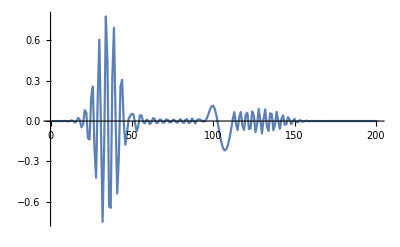

```mathematica
ListPlot[Re[psilist][[2000]],PlotRange->All,Joined->True]
```

```mathematica
Length[psilist]
```

2002

```mathematica
ListPlot3D[Re[psilist],PlotRange->All]
```

-Graphics3D-